```mathematica
(* set global assumptions *)
$Assumptions = {t ∈ Reals, J∈Reals,ν∈Reals,ν>0,γ∈Reals,γ>0,ω∈Reals,ω>=0}
numvals = {J->2,γ->1}
```

{t∈ℝ,J∈ℝ,ν∈ℝ,ν>0,γ∈ℝ,γ>0,ω∈ℝ,ω≥0}

{J→2,γ→1}

```mathematica
ν = 1
sol = DSolve[D[B[t],{t}] == -2*ν*B[t] +γ*J*Cos[ω*t],B[t],t]
```

1

{{B[t]→ⅇ^(-2 t) C[1]+(J γ (2 Cos[t ω]+ω Sin[t ω]))/(4+ω^2)}}

```mathematica
B[t]/.sol/.{t->0}
```

{(2 J γ)/(4+ω^2)+C[1]}

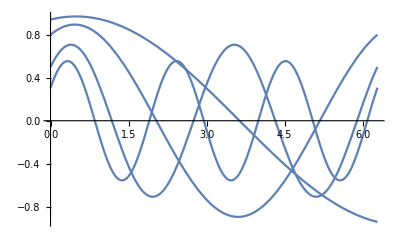

```mathematica
(* plot the solution *)
Plot[B[t]/.sol/.numvals/.{ω->{0.5,1,2,3},C[1]->0},{t,0,2*Pi}]
```

```mathematica
(* solve for a non-linear BH curve: ploy-2 *)
ν = 1/2+B[t]
solPoly2 = DSolve[D[B[t],{t}] == -2*ν*B[t] +γ*J*Cos[ω*t],B[t],t]
sPoly2 = FullSimplify[solPoly2/.{C[1]->0}]
```

1/2+B[t]

{{B[t]→(C[1] (-1/2 ⅇ^(-t/2) MathieuC[-1/ω^2,(4 J γ)/ω^2,(t ω)/2]+1/2 ⅇ^(-t/2) ω MathieuCPrime[-1/ω^2,(4 J γ)/ω^2,(t ω)/2])-1/2 ⅇ^(-t/2) MathieuS[-1/ω^2,(4 J γ)/ω^2,(t ω)/2]+1/2 ⅇ^(-t/2) ω MathieuSPrime[-1/ω^2,(4 J γ)/ω^2,(t ω)/2])/(2 (ⅇ^(-t/2) C[1] MathieuC[-1/ω^2,(4 J γ)/ω^2,(t ω)/2]+ⅇ^(-t/2) MathieuS[-1/ω^2,(4 J γ)/ω^2,(t ω)/2]))}}

{{B[t]→1/4 (-1+(ω MathieuSPrime[-1/ω^2,(4 J γ)/ω^2,(t ω)/2])/MathieuS[-1/ω^2,(4 J γ)/ω^2,(t ω)/2])}}

π/2

0

3

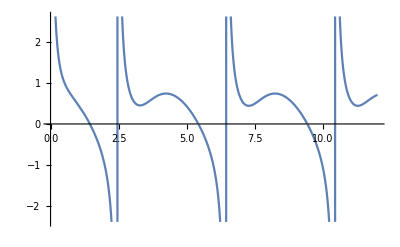

π

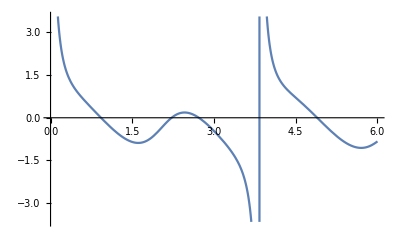

2 π

100

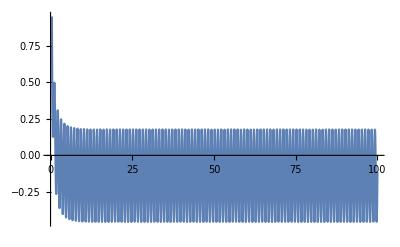

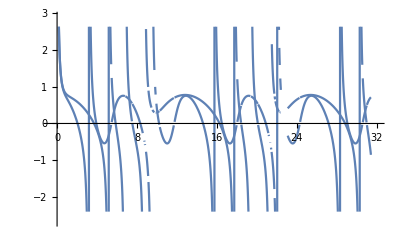

```mathematica
w = 2*Pi/4
n =0
np = 3
Plot[B[t]/.sPoly2/.numvals/.{ω->w},{t,n*2*Pi/w,(n+np)*2*Pi/w}]
w = 2*Pi/2
Plot[B[t]/.sPoly2/.numvals/.{ω->w},{t,n*2*Pi/w,(n+np)*2*Pi/w}]
w = 2*Pi
np=100
Plot[B[t]/.sPoly2/.numvals/.{ω->w},{t,n*2*Pi/w,(n+np)*2*Pi/w}]
```

```mathematica
0Cos[t ω]
```

```mathematica
0
```